```mathematica
(*Mathematica*)
```

```mathematica
Clear[t,a,p,aa,bb]
```

```mathematica
(* cf: A073058*)
```

```mathematica
(* F. M. Deking, "Recurrent Sets" ,Advances in Mathematics,vol. 44, no.1,April 1982, page 85, section 4.1*)
```

```mathematica
n0=4
```

4

```mathematica
(* substitution *)
```

```mathematica
s[1]={2,1,2,0}; s[2]={3,0,0,0}; s[3]={4,3,4,0}; s[4]={1,0,0,0};
```

```mathematica
(* make matrix*)
```

```mathematica
M=Table[Table[Count[s[j],i],{i,1,n0}],{j,1,n0}]
```

{{1,2,0,0},{0,0,1,0},{0,0,1,2},{1,0,0,0}}

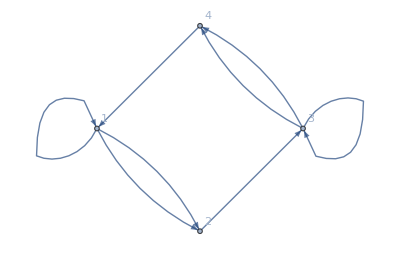

```mathematica
AdjacencyGraph[M,DirectedEdges->True,VertexLabels->"Name"]
```

```mathematica
(* make polynomial*)
```

```mathematica
Det[M-x*IdentityMatrix[n0]]
```

-4+x^2-2 x^3+x^4

```mathematica
(* solve Polynomial*)
```

```mathematica
NSolve[Det[M-x*IdentityMatrix[n0]]==0,x]
```

{{x→-1.},{x→0.5-1.32288 ⅈ},{x→0.5+1.32288 ⅈ},{x→2.}}

```mathematica
r[i_]:={Re[x],Im[x]}/.NSolve[Det[M-x*IdentityMatrix[n0]]==0,x][[i]]
```

```mathematica
Clear[s]
```

```mathematica
s[1]={2,1,2}; s[2]={3}; s[3]={4,3,4}; s[4]={1};
```

```mathematica
w=Flatten[Table[s[i],{i,4}]]
```

{2,1,2,3,4,3,4,1}

```mathematica
t[a_] :=Flatten[s/@a];
```

```mathematica
p[0]=w;p[1]=t[p[0]];
```

```mathematica
p[n_]:=t[p[n-1]]
```

```mathematica
aa=p[16];
```

```mathematica
Length[aa]
```

524288

```mathematica
bb=aa/. 1->{1,0} /. 2->{0,1} /. 3->{-1,0} /. 4->{0,-1} ;
```

```mathematica
cc=FoldList[Plus,{0,0},bb];
```

```mathematica
g1=ListPlot[cc,PlotRange->All,ColorFunction->Hue,Axes->False,ImageSize->2000,PlotStyle->PointSize[0.001]];
```

```mathematica
Clear[t,a,p,aa,bb]
```

```mathematica
(* cf: A073058*)
```

```mathematica
(* F. M. Deking, "Recurrent Sets" ,Advances in Mathematics,vol. 44, no.1,April 1982, page 85, section 4.1*)
```

```mathematica
n0=4
```

4

```mathematica
(* substitution *)
```

```mathematica
s[1]={2,1,2,0}; s[2]={3,3,0,0}; s[3]={4,3,4,0}; s[4]={1,1,0,0};
```

```mathematica
(* make matrix*)
```

```mathematica
M=Table[Table[Count[s[j],i],{i,1,n0}],{j,1,n0}]
```

{{1,2,0,0},{0,0,2,0},{0,0,1,2},{2,0,0,0}}

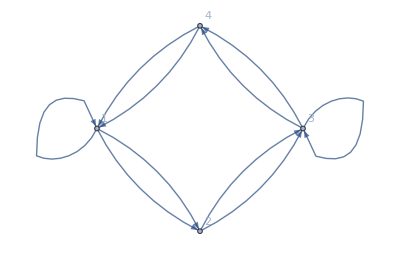

```mathematica
AdjacencyGraph[M,DirectedEdges->True,VertexLabels->"Name"]
```

```mathematica
(* make polynomial*)
```

```mathematica
Det[M-x*IdentityMatrix[n0]]
```

-16+x^2-2 x^3+x^4

```mathematica
(* solve Polynomial*)
```

```mathematica
r[i_]:={Re[x],Im[x]}/.NSolve[Det[M-x*IdentityMatrix[n0]]==0,x][[i]]
```

```mathematica
Clear[s]
```

```mathematica
s[1]={2,1,2}; s[2]={3,3}; s[3]={4,3,4}; s[4]={1,1};
```

```mathematica
w=Flatten[Table[s[i],{i,4}]]
```

{2,1,2,3,3,4,3,4,1,1}

```mathematica
t[a_] :=Flatten[s/@a];
```

```mathematica
p[0]=w;p[1]=t[p[0]];
```

```mathematica
p[n_]:=t[p[n-1]]
```

```mathematica
aa=p[10];
```

```mathematica
Length[aa]
```

122754

```mathematica
bb=aa/. 1->{1,0} /. 2->{0,1} /. 3->{-1,0} /. 4->{0,-1} ;
```

```mathematica
cc=FoldList[Plus,{0,0},bb];
```

```mathematica
g2=ListPlot[cc,PlotRange->All,ColorFunction->Hue,Axes->False,ImageSize->2000,PlotStyle->PointSize[0.001]];
```

```mathematica
Clear[t,a,p,aa,bb]
```

```mathematica
(* cf: A073058*)
```

```mathematica
(* F. M. Deking, "Recurrent Sets" ,Advances in Mathematics,vol. 44, no.1,April 1982, page 85, section 4.1*)
```

```mathematica
n0=4
```

4

```mathematica
(* substitution *)
```

```mathematica
s[1]={2,1,1,2}; s[2]={3,3,0,0}; s[3]={4,3,3,4}; s[4]={1,1,0,0};
```

```mathematica
(* make matrix*)
```

```mathematica
M=Table[Table[Count[s[j],i],{i,1,n0}],{j,1,n0}]
```

{{2,2,0,0},{0,0,2,0},{0,0,2,2},{2,0,0,0}}

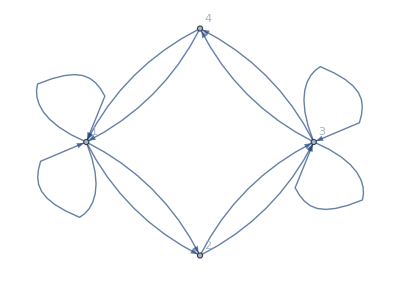

```mathematica
AdjacencyGraph[M,DirectedEdges->True,VertexLabels->"Name"]
```

```mathematica
(* make polynomial*)
```

```mathematica
Det[M-x*IdentityMatrix[n0]]
```

-16+4 x^2-4 x^3+x^4

```mathematica
(* solve Polynomial*)
```

```mathematica
NSolve[Det[M-x*IdentityMatrix[n0]]==0,x]
```

{{x→-1.23607},{x→1.-1.73205 ⅈ},{x→1.+1.73205 ⅈ},{x→3.23607}}

```mathematica
r[i_]:={Re[x],Im[x]}/.NSolve[Det[M-x*IdentityMatrix[n0]]==0,x][[i]]
```

```mathematica
Clear[s]
```

```mathematica
s[1]={2,1,1,2}; s[2]={3,3}; s[3]={4,3,3,4}; s[4]={1,1};
```

```mathematica
w=Flatten[Table[s[i],{i,4}]]
```

{2,1,1,2,3,3,4,3,3,4,1,1}

```mathematica
t[a_] :=Flatten[s/@a];
```

```mathematica
p[0]=w;p[1]=t[p[0]];
```

```mathematica
p[n_]:=t[p[n-1]]
```

```mathematica
aa=p[9];
```

```mathematica
Length[aa]
```

477184

```mathematica
bb=aa/. 1->{1,0} /. 2->{0,1} /. 3->{-1,0} /. 4->{0,-1} ;
```

```mathematica
cc=FoldList[Plus,{0,0},bb];
```

```mathematica
g3=ListPlot[cc,PlotRange->All,ColorFunction->Hue,Axes->False,ImageSize->2000,PlotStyle->PointSize[0.001]];
```

```mathematica
Clear[t,a,p,aa,bb]
```

```mathematica
(* cf: A073058*)
```

```mathematica
(* F. M. Deking, "Recurrent Sets" ,Advances in Mathematics,vol. 44, no.1,April 1982, page 85, section 4.1*)
```

```mathematica
n0=4
```

4

```mathematica
(* substitution *)
```

```mathematica
s[1]={2,1,2,0}; s[2]={3,3,3,0}; s[3]={4,3,4,0}; s[4]={1,1,1,0};
```

```mathematica
(* make matrix*)
```

```mathematica
M=Table[Table[Count[s[j],i],{i,1,n0}],{j,1,n0}]
```

{{1,2,0,0},{0,0,3,0},{0,0,1,2},{3,0,0,0}}

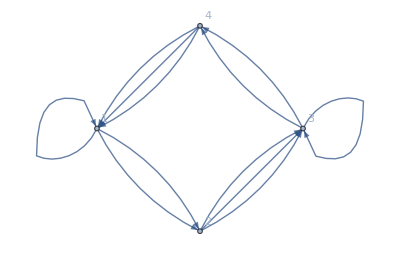

```mathematica
AdjacencyGraph[M,DirectedEdges->True,VertexLabels->"Name"]
```

```mathematica
(* make polynomial*)
```

```mathematica
Det[M-x*IdentityMatrix[n0]]
```

-36+x^2-2 x^3+x^4

```mathematica
(* solve Polynomial*)
```

```mathematica
NSolve[Det[M-x*IdentityMatrix[n0]]==0,x]
```

{{x→-2.},{x→0.5-2.39792 ⅈ},{x→0.5+2.39792 ⅈ},{x→3.}}

```mathematica
r[i_]:={Re[x],Im[x]}/.NSolve[Det[M-x*IdentityMatrix[n0]]==0,x][[i]]
```

```mathematica
Clear[s]
```

```mathematica
s[1]={2,1,2}; s[2]={3,3,3}; s[3]={4,3,4}; s[4]={1,1,1};
```

```mathematica
w=Flatten[Table[s[i],{i,4}]]
```

{2,1,2,3,3,3,4,3,4,1,1,1}

```mathematica
t[a_] :=Flatten[s/@a];
```

```mathematica
p[0]=w;p[1]=t[p[0]];
```

```mathematica
p[n_]:=t[p[n-1]]
```

```mathematica
aa=p[10];
```

```mathematica
Length[aa]
```

708588

```mathematica
bb=aa/. 1->{1,0} /. 2->{0,1} /. 3->{-1,0} /. 4->{0,-1} ;
```

```mathematica
cc=FoldList[Plus,{0,0},bb];
```

```mathematica
g4=ListPlot[cc,PlotRange->All,ColorFunction->Hue,Axes->False,ImageSize->2000,PlotStyle->PointSize[0.001]];
```

```mathematica
Export["4dragons_4symbols_substitutions.jpg",GraphicsGrid[{{g1,g2},{g3,g4}},ImageSize->{{4000,4000}}]]
(*end*)
```

4dragons_4symbols_substitutions.jpg